## Symmetric Detuning

```mathematica
(*probs1 = {10.805152806772494,19.279523102069422,10.805152806772494,23.516874171171818,17.161015364553336,15.042444816992372,36.228816985580416,48.94067760232554,58.4746416095189,53.17797438680317,49.99999999999999,49.99999999999999,49.99999999999999,31.991551032058656,17.161015364553336,7.627211845746573,16.1017159275579,12.923684864026255,17.161015364553336,5.508513411558081,9.74569089638299}/100;*)
probs1 = {4.449263018825566,22.457622581492544,22.457622581492544,12.923684864026255,8.686328263359592,4.449263018825566,30.932232863236937,44.70336089066096,48.94067760232554,37.28823258189421,45.76269452488014,44.70336089066096,46.82202561319685,37.28823258189421,15.042444816992372,6.567773472461323,18.22034081392916,19.279523102069422,12.923684864026255,17.161015364553336,4.449263018825566}/100;
(*probs1 = {2.863148609143641,6.005602932936389,7.053061853858771,15.433026170083524,17.527875828485342,6.005602932936389,7.053061853858771,32.192764755437665,42.66754426382388,50.000000000000014,39.52520298949221,36.38268486750442,43.71504055487366,45.810037727398694,16.480467510767802,4.958118308478076,9.14805688824063,17.527875828485342}/100;
probs1 = {21.717861290422118,15.433026170083524,6.005602932936389,7.053061853858771,17.527875828485342,46.85753325526598,52.094974884232556,47.90502511576747,44.76253945033704,52.094974884232556,34.287723079024595,42.66754426382388,23.812720819779482,2.863148609143641,11.243102699067094,14.385623103563756}/100;*)
symdet = -2 321;
symstep = 321/5;
symlist1 = 2 π Table[i symstep + symdet, {i, 0, Length[probs1] -1}];
data = Transpose[{symlist1, probs1}];
```

```mathematica
α[t_, δ_, Ω_, η_] := - ⅈ (η Ω)/(2 δ)(Exp[ⅈ δ t] - 1)
catfun[t_, δ_, Ω_, η_, nbar_ , δ0_, A_, B_] := A 1/2(1 - Exp[- 2 Abs[α[t, δ + δ0, Ω, η]]^2 (1 + 2nbar)])  + B
```

```mathematica
η = 0.0053;
Ω =  2 π 30 10^3;
nbar = 0;
δth = 2 η Ω;
tgate = (2 π)/δth;
fit = NonlinearModelFit[data, {catfun[tgate, δ, η, Ω, 0.3, δ0, 1, 0] ,0≤ A≤ 1 , 0≤ B≤ .2}, {{Ω0, 30 10^3},{nb, 0.3},{δ0, 20}, {A,.8}, {B, 0.1}}, δ];
fit["BestFitParameters"]
Ω0/(2 π)/.fit["BestFitParameters"]
```

{Ω0→30000.,nb→0.3,δ0→148.621,A→0.719854,B→0.1}

4774.65

```mathematica
148.621/(2 π)
```

23.6538

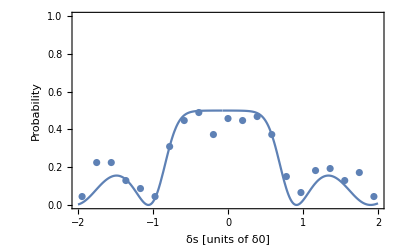

```mathematica
dataplot = Transpose[{symlist1/(2 π 330), probs1}];
Show[Plot[fit[ 2 π δ 322 ], {δ, -2 ,2}],
ListPlot[dataplot], 
Frame-> True, PlotRange-> {All, {0,1}}, Axes-> False, FrameStyle-> Directive[Black, 14], FrameLabel-> {"δs [units of δ0] ", "Probability"}]
```

## Time Detuning

```mathematica
probs2= {0.000596086098654914,12.290598868415264,25.907827376299398,28.002640914535267,25.907827376299398,9.14805688824063,2.863148609143641,19.623049767995433,23.812720819779482,12.290598868415264,10.195471286962785,16.480467510767802,18.575419713317253,23.812720819779482,19.623049767995433}/100;

tstep = 2 15 16.72 10^-6;
timelist1 = Table[i tstep, {i, 0, Length[probs2] -1}] //N
timedata = Transpose[{timelist1, probs2}];
```

{0.,0.0005016,0.0010032,0.0015048,0.0020064,0.002508,0.0030096,0.0035112,0.0040128,0.0045144,0.005016,0.0055176,0.0060192,0.0065208,0.0070224}

```mathematica
α[t_, δ_, Ω_, η_] := - ⅈ (η Ω)/(2 δ)(Exp[ⅈ δ t] - 1)
catfun[t_, δ_, Ω_, η_, nbar_ , δ0_, A_, B_] := A 1/2(1 - Exp[- 2 Abs[α[t, δ + δ0, Ω, η]]^2 (1 + 2nbar)])  + B
η = 0.0053;
Ω =  2 π 30 10^3;
nbar = 0;
δth = 2 η Ω;
tgate = (2 π)/δth
timefit = NonlinearModelFit[timedata, {catfun[t,δth, Ω, η, nb, 0, 1, 0] ,0≤ A≤ 1 , 0≤ B≤ .2, nb≥ 0}, {{Ω0, 30 10^3},{nb, 1},{δ0, 20}, {A,.8}, {B, 0.1}}, t];
fit["BestFitParameters"]
```

0.00314465

{Ω0→30000.,nb→0.3,δ0→148.621,A→0.719854,B→0.1}

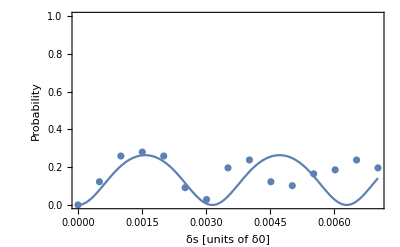

```mathematica
timedataplot = Transpose[{timelist1 , probs2}];
Show[Plot[timefit[t], {t, 0 ,Last[timelist1]}],
ListPlot[timedataplot], 
Frame-> True, PlotRange-> {All, {0,1}}, Axes-> False, FrameStyle-> Directive[Black, 14], FrameLabel-> {"δs [units of δ0] ", "Probability"}]
```